# Figure 6: SCSS Breeding Finite Resolution Homodyne Measurement

Here we validate our approximation, for exact SCSS breeding, that the mixed state resulting from a homodyne measurement outcome p,  with finite resolution  2ε below a certain threshold, is well represented by the pure state resulting from an infinite resolution homodyne measurement outcome p. To do this we calculate the fidelity between the pure SCSS breeding output state, Tildeϕropt(q1|p), and the mixed SCSS breeding output state Tildeρropt (q1, q1’, ε|p) as a function of ε for n ∈ {10, 40} and p ∈ {0, Sqrt(π), 2*Sqrt(π)}.

The unnormalized even SCSS breeding output state, TildeΦ(q|p), and its complex conjugate,TildeΦStar(q|p) , are

```mathematica
TildeΦEven=(ⅇ^(-1/2 ⅇ^(-2 r) (ⅈ p+ⅇ^(2 r) q) (-ⅈ p+ⅇ^(2 r) (4 √π+q))) (ⅇ^(2 ⅈ p √π)+ⅇ^(2 ⅇ^(2 r) √π (√π+q))+ⅇ^(2 √π (ⅈ p+2 ⅇ^(2 r) q))+ⅇ^(2 √π (2 ⅈ p+ⅇ^(2 r) (√π+q)))))/(2 (1+ⅇ^(2 ⅇ^(2 r) π)) √π);
TildeΦStarEven=(ⅇ^(-1/2 ⅇ^(-2 r) (-ⅈ p+ⅇ^(2 r) q) (ⅈ p+ⅇ^(2 r) (4 √π+q))) (ⅇ^(-2 ⅈ p √π)+ⅇ^(2 ⅇ^(2 r) √π (√π+q))+ⅇ^(2 √π (-ⅈ p+2 ⅇ^(2 r) q))+ⅇ^(2 √π (-2 ⅈ p+ⅇ^(2 r) (√π+q)))))/(2 (1+ⅇ^(2 ⅇ^(2 r) π)) √π);
```

The normalized even SCSS breeding output states associated with measurement outcomes p ∈ {0, Sqrt(π), 2*Sqrt(π)} are the same and given by

```mathematica
Tildeφ=(Exp[(-Exp[2*r]*(q+2*Sqrt[Pi])^2)/2]+2*Exp[(-Exp[2*r]*q^2)/2]+Exp[(-Exp[2*r]*(q-2*Sqrt[Pi])^2)/2])/(Pi^(1/4)*Sqrt[2*Exp[-r]*(3+Exp[-4*Exp[2*r]*Pi]+4*Exp[-Exp[2*r]*Pi])]);
```

## p = 0 Mixed State

To find the mixed state associated with a finite resolution,  2ε, homodyne measurement centered around p = 0 we first integrate TildeΦ(q|p)*TildeΦ*(q’|p)  from -ε to ε

```mathematica
(*TildeΓp0 = Integrate[TildeΦEven*(TildeΦStarEven/.q->qPrime),{p,-ε,ε},Assumptions->{q ∈ Reals,k ∈ Integers,qPrime ∈ Reals,ε ∈ Reals, n ∈ Integers,r>0}];*)
TildeΓp0 = 1/(4 (1+ⅇ^(2 ⅇ^(2 r) π))^2 √π)ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+r) ((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r ε]+ⅈ ((ⅇ^(ⅇ^(2 r) √π (√π+2 q))+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime))) Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]));
```

The probability of obtaining a measurement outcome between  -ε to ε, TildePp0ε, is the normalization constant of TildeΓp0 and is found by integrating TildeΓp0 over all phase space

```mathematica
(*TildePp0ε = Integrate[Simplify[(TildeΓp0/.qPrime->q)],{q,-∞,∞},Assumptions->{ε >0,r>0}];*)
TildePp0ε = ((2+4 ⅇ^(4 ⅇ^(2 r) π)) Erf[ⅇ^-r ε]+ⅈ (Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]+4 ⅇ^(2 ⅇ^(2 r) π) (Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε])-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]))/(4 (1+ⅇ^(2 ⅇ^(2 r) π))^2);
```

The normalized mixed state is then the unnormalized state divided by the probability

```mathematica
(*Tildeρp0 =  FullSimplify[TildeΓp0/TildePp0ε,Assumptions->{q∈ Reals,qPrime ∈ Reals, ε ∈ Reals}];*)
Tildeρp0 = (ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+r) ((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r ε]+ⅈ ((ⅇ^(ⅇ^(2 r) √π (√π+2 q))+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime))) Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε])))/(√π ((2+4 ⅇ^(4 ⅇ^(2 r) π)) Erf[ⅇ^-r ε]+ⅈ (Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]+4 ⅇ^(2 ⅇ^(2 r) π) (Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε])-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε])));
```

Calculating the fidelity between the normalized mixed state and pure state as a function of ε and r

```mathematica
(*Fp0 =Simplify[ Integrate[Tildeρp0*(Tildeφ*(Tildeφ/q->qPrime)),{q,-∞,∞},{qPrime,-∞,∞},Assumptions->{ε>0,r>0}],Assumptions->{ε>0,r>0}];*)
Fp0 = (ⅇ^(-2 (2 ⅇ^(2 r) π+r)) (Erf[ⅇ^-r ε] MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]^2+4 MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2] (ⅇ^r π^(3/2) ((-2-2 ⅇ^(3 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π)+2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r ε]-ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) (Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]))+ⅇ^(ⅇ^(2 r) π) (2 ⅇ^(ⅇ^(2 r) π) Erf[ⅇ^-r ε]+ⅈ (Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2])+4 (ⅇ^(2 r) π^3 ((4+8 ⅇ^(3 ⅇ^(2 r) π)+4 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π)+12 ⅇ^(7 ⅇ^(2 r) π)+9 ⅇ^(8 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π) Erf[ⅇ^r √π]^2-2 ⅇ^(4 ⅇ^(2 r) π) (2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)) Erf[2 ⅇ^r √π]+ⅇ^(8 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]^2+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π])) Erf[ⅇ^-r ε]-ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) (2 (-2-2 ⅇ^(3 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π)+2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]+(-1-2 ⅇ^(ⅇ^(2 r) π)+Erf[ⅇ^r √π]) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]+4 Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]+2 ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]-Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]))+2 ⅇ^(ⅇ^(2 r) π+r) π^(3/2) (2 ⅇ^(ⅇ^(2 r) π) (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+3 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r ε]+ⅈ ((-2-4 ⅇ^(3 ⅇ^(2 r) π)-5 ⅇ^(4 ⅇ^(2 r) π)+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]+(-1-2 ⅇ^(ⅇ^(2 r) π)+Erf[ⅇ^r √π]) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]+2 Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+5 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]+Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]+2 ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε]-Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]+(6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^-r ε]+ⅈ (4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]+Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε]-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]^2)))/(8 (3+ⅇ^(-4 ⅇ^(2 r) π)+4 ⅇ^(-ⅇ^(2 r) π)) π^3 ((2+4 ⅇ^(4 ⅇ^(2 r) π)) Erf[ⅇ^-r ε]+ⅈ (Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r ε]+4 ⅇ^(2 ⅇ^(2 r) π) (Erfi[ⅇ^r √π-ⅈ ⅇ^-r ε]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r ε])-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r ε])));
```

## p = Sqrt(π) Mixed State

To find the mixed state associated with a finite resolution,  2ε, homodyne measurement centered around p = Sqrt(π) we first integrate TildeΦ(q|p)*TildeΦ*(q’|p)  from Sqrt(π)-ε to Sqrt(π)+ε

```mathematica
(*TildeΓpSqrtPi = Integrate[TildeΦEven*(TildeΦStarEven/.q->qPrime),{p,Sqrt[Pi]-ε,Sqrt[Pi]+ε},Assumptions->{q ∈ Reals,k ∈ Integers,qPrime ∈ Reals,ε ∈ Reals, n ∈ Integers,r>0}];*)
TildeΓpSqrtPi = 1/(8 (1+ⅇ^(2 ⅇ^(2 r) π))^2 √π)ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+r) (-((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (√π-ε)])+(1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (√π+ε)]+ⅈ ((ⅇ^(ⅇ^(2 r) √π (√π+2 q))+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime))) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) (Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]));
```

The probability of obtaining a measurement outcome between  Sqrt(π)-ε to Sqrt(π)+ε, TildePpSqrtPiε, is the normalization constant of TildeΓpSqrtPi and is found by integrating TildeΓpSqrtPi over all phase space

```mathematica
(*TildePpSqrtPiε = Integrate[Simplify[(TildeΓpSqrtPi/.qPrime->q)],{q,-∞,∞},Assumptions->{ε >0,r>0}];*)
TildePpSqrtPiε = 1/(16 (1+ⅇ^(2 ⅇ^(2 r) π))^2 π^(3/2))ⅇ^-r (2 ⅇ^r π^(3/2) ((-2-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π-ε)]+(2+3 ⅇ^(4 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π+ε)]+Erf[ⅇ^-r ((1+2 ⅈ ⅇ^(2 r)) √π+ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅈ Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅈ Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])+(Erf[ⅇ^-r (√π-ε)]-Erf[ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]-4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]);
```

The normalized mixed state is then the unnormalized state divided by the probability

```mathematica
(*TildeρpSqrtPi =  FullSimplify[TildeΓpSqrtPi/TildePpSqrtPiε,Assumptions->{q∈ Reals,qPrime ∈ Reals, ε ∈ Reals}];*)
TildeρpSqrtPi = (2 ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+2 r) π (-((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (√π-ε)])+(1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (√π+ε)]+ⅈ ((ⅇ^(ⅇ^(2 r) √π (√π+2 q))+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime))+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime))) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) (Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])))/(2 ⅇ^r π^(3/2) (-2 Erf[ⅇ^-r (√π-ε)]+2 Erf[ⅇ^-r (√π+ε)]+Erf[ⅇ^-r ((1+2 ⅈ ⅇ^(2 r)) √π+ε)]+ⅇ^(4 ⅇ^(2 r) π) (2+Erfc[2 ⅇ^r √π]) (-1+Erf[ⅇ^-r (√π+ε)]+Erfc[ⅇ^-r (√π-ε)])-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) (-1+Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])+ⅈ (Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]))+(Erf[ⅇ^-r (√π-ε)]-Erf[ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]-4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]);
```

Calculating the fidelity between the normalized mixed state and pure state as a function of ε and r

```mathematica
(*FpSqrtPi =Simplify[ Integrate[TildeρpSqrtPi*(Tildeφ*(Tildeφ/q->qPrime)),{q,-∞,∞},{qPrime,-∞,∞},Assumptions->{ε>0,r>0}],Assumptions->{ε>0,r>0}];*)
FpSqrtPi= (ⅇ^(-4 ⅇ^(2 r) π-r) ((-Erf[ⅇ^-r (√π-ε)]+Erf[ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]^2-4 MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2] (ⅇ^r π^(3/2) ((-2-2 ⅇ^(3 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π)+2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π-ε)]+(2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)-2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]-ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π+ε)]+ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]))+ⅇ^(ⅇ^(2 r) π) (2 ⅇ^(ⅇ^(2 r) π) Erf[ⅇ^-r (√π-ε)]-2 ⅇ^(ⅇ^(2 r) π) Erf[ⅇ^-r (√π+ε)]-ⅈ (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2])-4 (ⅇ^(2 r) π^3 ((4+8 ⅇ^(3 ⅇ^(2 r) π)+4 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π)+12 ⅇ^(7 ⅇ^(2 r) π)+9 ⅇ^(8 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π) Erf[ⅇ^r √π]^2-2 ⅇ^(4 ⅇ^(2 r) π) (2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)) Erf[2 ⅇ^r √π]+ⅇ^(8 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]^2+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π])) Erf[ⅇ^-r (√π-ε)]-(4+8 ⅇ^(3 ⅇ^(2 r) π)+4 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π)+12 ⅇ^(7 ⅇ^(2 r) π)+9 ⅇ^(8 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π) Erf[ⅇ^r √π]^2-2 ⅇ^(4 ⅇ^(2 r) π) (2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)) Erf[2 ⅇ^r √π]+ⅇ^(8 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]^2+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π])) Erf[ⅇ^-r (√π+ε)]+ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) (2 (-2-2 ⅇ^(3 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π)+2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+(-1-2 ⅇ^(ⅇ^(2 r) π)+Erf[ⅇ^r √π]) Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]+4 Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]-Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]-4 Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-2 ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+4 Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+2 ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]))+2 ⅇ^(ⅇ^(2 r) π+r) π^(3/2) (2 ⅇ^(ⅇ^(2 r) π) (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+3 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π-ε)]+(4 ⅇ^(ⅇ^(2 r) π)+6 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(5 ⅇ^(2 r) π)-6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^r √π]-2 ⅇ^(5 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (√π+ε)]+Erf[ⅇ^-r ((1+2 ⅈ ⅇ^(2 r)) √π+ε)]+2 ⅈ Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅈ Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅈ Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅈ Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-ⅈ Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-2 ⅈ Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-ⅈ Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]-2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+ⅈ Erf[ⅇ^r √π] Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]+(6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^-r (√π-ε)]+Erf[ⅇ^-r ((1-2 ⅈ ⅇ^(2 r)) √π-ε)]+Erf[ⅇ^-r ((1+2 ⅈ ⅇ^(2 r)) √π-ε)]-6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^-r (√π+ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-ⅈ Erfi[2 ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]+ⅈ Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]^2)))/(4 (3+ⅇ^(-4 ⅇ^(2 r) π)+4 ⅇ^(-ⅇ^(2 r) π)) π^(3/2) (2 ⅇ^r π^(3/2) (-2 Erf[ⅇ^-r (√π-ε)]+2 Erf[ⅇ^-r (√π+ε)]+Erf[ⅇ^-r ((1+2 ⅈ ⅇ^(2 r)) √π+ε)]+ⅇ^(4 ⅇ^(2 r) π) (2+Erfc[2 ⅇ^r √π]) (-1+Erf[ⅇ^-r (√π+ε)]+Erfc[ⅇ^-r (√π-ε)])-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) (-1+Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)])+ⅈ (Erfi[ⅇ^-r ((ⅈ+2 ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+2 ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[2 ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]))+(Erf[ⅇ^-r (√π-ε)]-Erf[ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]-4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^r √π-ⅈ ⅇ^-r (√π+ε)]-Erfi[ⅇ^r √π+ⅈ ⅇ^-r (√π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]));
```

## p = 2*Sqrt(π) Mixed State

To find the mixed state associated with a finite resolution,  2ε, homodyne measurement centered around p = 2*Sqrt(π) we first integrate TildeΦ(q|p)*TildeΦ*(q’|p)  from 2*Sqrt(π)-ε to 2*Sqrt(π)+ε

```mathematica
(*TildeΓp2SqrtPi = Integrate[TildeΦEven*(TildeΦStarEven/.q->qPrime),{p,2*Sqrt[Pi]-ε,2*Sqrt[Pi]+ε},Assumptions->{q ∈ Reals,k ∈ Integers,qPrime ∈ Reals,ε ∈ Reals, n ∈ Integers,r>0}];*)
TildeΓp2SqrtPi = 1/(8 (1+ⅇ^(2 ⅇ^(2 r) π))^2 √π)ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+r) ((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (-2 √π+ε)]+(1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (2 √π+ε)]+ⅈ (ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]));
```

The probability of obtaining a measurement outcome between  2*Sqrt(π)-ε to 2*Sqrt(π)+ε, TildePp2SqrtPiε, is the normalization constant of TildeΓp2SqrtPi and is found by integrating TildeΓp2SqrtPi over all phase space

```mathematica
(*TildePp2SqrtPiε = Integrate[Simplify[(TildeΓp2SqrtPi/.qPrime->q)],{q,-∞,∞},Assumptions->{ε >0,r>0}];*)
TildePp2SqrtPiε = 1/(16 (1+ⅇ^(2 ⅇ^(2 r) π))^2 π^(3/2))ⅇ^-r (2 ⅇ^r π^(3/2) ((-2-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π-ε)]+(2+3 ⅇ^(4 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π+ε)]+Erf[ⅇ^-r ((2+2 ⅈ ⅇ^(2 r)) √π+ε)]+ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅈ ⅇ^(2 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])+(Erf[ⅇ^-r (2 √π-ε)]-Erf[ⅇ^-r (2 √π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]-4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]);
```

The normalized mixed state is then the unnormalized state divided by the probability

```mathematica
(*Tildeρp2SqrtPi =  FullSimplify[TildeΓp2SqrtPi/TildePp2SqrtPiε,Assumptions->{q∈ Reals,qPrime ∈ Reals, ε ∈ Reals}];*)
Tildeρp2SqrtPi = (2 ⅇ^(-1/2 ⅇ^(2 r) (q^2+qPrime^2+4 √π (q+qPrime))+2 r) π (-((1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (-2 √π+ε)])-(1+ⅇ^(4 ⅇ^(2 r) √π q)+ⅇ^(4 ⅇ^(2 r) √π qPrime)+ⅇ^(4 ⅇ^(2 r) √π (q+qPrime))+2 ⅇ^(2 ⅇ^(2 r) √π (2 √π+q+qPrime))) Erf[ⅇ^-r (2 √π+ε)]-ⅈ (ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(2 ⅇ^(2 r) √π (q+qPrime)) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅇ^(ⅇ^(2 r) √π (√π+2 q+4 qPrime)) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])-ⅇ^(ⅇ^(2 r) √π (√π+2 q)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅇ^(ⅇ^(2 r) √π (√π+4 q+2 qPrime)) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])))/(-2 ⅇ^r π^(3/2) (-2 Erf[ⅇ^-r (2 √π-ε)]+2 Erf[ⅇ^-r (2 √π+ε)]+Erf[ⅇ^-r ((2+2 ⅈ ⅇ^(2 r)) √π+ε)]+ⅇ^(4 ⅇ^(2 r) π) (2+Erfc[2 ⅇ^r √π]) (-1+Erf[ⅇ^-r (2 √π+ε)]+Erfc[ⅇ^-r (2 √π-ε)])+ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) (-1+Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]))+(-Erf[ⅇ^-r (2 √π-ε)]+Erf[ⅇ^-r (2 √π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]+4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]);
```

Calculating the fidelity between the normalized mixed state and pure state as a function of ε and r

```mathematica
(*Fp2SqrtPi =Simplify[ Integrate[Tildeρp2SqrtPi*(Tildeφ*(Tildeφ/q->qPrime)),{q,-∞,∞},{qPrime,-∞,∞},Assumptions->{ε>0,r>0}],Assumptions->{ε>0,r>0}];*)
Fp2SqrtPi= -((ⅇ^(-4 ⅇ^(2 r) π-r) ((-Erf[ⅇ^-r (2 √π-ε)]+Erf[ⅇ^-r (2 √π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]^2-4 MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2] (ⅇ^r π^(3/2) ((-2-2 ⅇ^(3 ⅇ^(2 r) π)-ⅇ^(4 ⅇ^(2 r) π)+2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π-ε)]+(2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)-2 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]-ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π+ε)]+ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]))+ⅇ^(ⅇ^(2 r) π) (2 ⅇ^(ⅇ^(2 r) π) Erf[ⅇ^-r (2 √π-ε)]-2 ⅇ^(ⅇ^(2 r) π) Erf[ⅇ^-r (2 √π+ε)]-ⅈ (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2])-4 (ⅇ^(2 r) π^3 ((4+8 ⅇ^(3 ⅇ^(2 r) π)+4 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π)+12 ⅇ^(7 ⅇ^(2 r) π)+9 ⅇ^(8 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π) Erf[ⅇ^r √π]^2-2 ⅇ^(4 ⅇ^(2 r) π) (2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)) Erf[2 ⅇ^r √π]+ⅇ^(8 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]^2+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π])) Erf[ⅇ^-r (2 √π-ε)]-(4+8 ⅇ^(3 ⅇ^(2 r) π)+4 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π)+12 ⅇ^(7 ⅇ^(2 r) π)+9 ⅇ^(8 ⅇ^(2 r) π)+6 ⅇ^(6 ⅇ^(2 r) π) Erf[ⅇ^r √π]^2-2 ⅇ^(4 ⅇ^(2 r) π) (2+2 ⅇ^(3 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π)) Erf[2 ⅇ^r √π]+ⅇ^(8 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]^2+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π])) Erf[ⅇ^-r (2 √π+ε)]+ⅈ ⅇ^(2 ⅇ^(2 r) π) (1+2 ⅇ^(ⅇ^(2 r) π)-Erf[ⅇ^r √π]) ((-1-2 ⅇ^(ⅇ^(2 r) π)+Erf[ⅇ^r √π]) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+(-1-2 ⅇ^(ⅇ^(2 r) π)+Erf[ⅇ^r √π]) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+2 ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]))+2 ⅇ^(ⅇ^(2 r) π+r) π^(3/2) (2 ⅇ^(ⅇ^(2 r) π) (-2-3 ⅇ^(3 ⅇ^(2 r) π)-3 ⅇ^(4 ⅇ^(2 r) π)+3 ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π]+ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π-ε)]+(4 ⅇ^(ⅇ^(2 r) π)+6 ⅇ^(4 ⅇ^(2 r) π)+6 ⅇ^(5 ⅇ^(2 r) π)-6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^r √π]-2 ⅇ^(5 ⅇ^(2 r) π) Erf[2 ⅇ^r √π]) Erf[ⅇ^-r (2 √π+ε)]+Erf[ⅇ^-r ((2+2 ⅈ ⅇ^(2 r)) √π+ε)]+2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+2 ⅈ Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(ⅇ^(2 r) π) Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ Erf[ⅇ^r √π] Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-5 ⅈ ⅇ^(4 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+4 ⅈ ⅇ^(3 ⅇ^(2 r) π) Erf[ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]+ⅈ ⅇ^(4 ⅇ^(2 r) π) Erf[2 ⅇ^r √π] Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]+(6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^-r (2 √π-ε)]-6 ⅇ^(4 ⅇ^(2 r) π) Erf[ⅇ^-r (2 √π+ε)]-ⅈ (Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-4 ⅇ^(3 ⅇ^(2 r) π) Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)])) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2]^2)))/(4 (3+ⅇ^(-4 ⅇ^(2 r) π)+4 ⅇ^(-ⅇ^(2 r) π)) π^(3/2) (-2 ⅇ^r π^(3/2) (-2 Erf[ⅇ^-r (2 √π-ε)]+2 Erf[ⅇ^-r (2 √π+ε)]+Erf[ⅇ^-r ((2+2 ⅈ ⅇ^(2 r)) √π+ε)]+ⅇ^(4 ⅇ^(2 r) π) (2+Erfc[2 ⅇ^r √π]) (-1+Erf[ⅇ^-r (2 √π+ε)]+Erfc[ⅇ^-r (2 √π-ε)])+ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (-ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-ⅈ Erfi[ⅇ^-r (2 (ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-2 ⅈ ⅇ^(2 ⅇ^(2 r) π) (-1+Erf[ⅇ^r √π]) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]))+(-Erf[ⅇ^-r (2 √π-ε)]+Erf[ⅇ^-r (2 √π+ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-2 ⅇ^r √π,1/2]+4 ⅈ ⅇ^(ⅇ^(2 r) π) (Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]+Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π-ⅈ ε)]-Erfi[ⅇ^-r ((-2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]-Erfi[ⅇ^-r ((2 ⅈ+ⅇ^(2 r)) √π+ⅈ ε)]) MeijerG[{{1},{}},{{1/2,1},{}},-ⅇ^r √π,1/2])));
```

## Plots

```mathematica
Fp010  = Fp0/.r->1/2 ArcSech[2*Pi/10];
Fp040  = Fp0/.r->1/2 ArcSech[2*Pi/40];
FpSqrtPi10  = FpSqrtPi/.r->1/2 ArcSech[2*Pi/10];
FpSqrtPi40   = FpSqrtPi/.r->1/2 ArcSech[2*Pi/40];
Fp2SqrtPi10  = Fp2SqrtPi/.r->1/2 ArcSech[2*Pi/10];
Fp2SqrtPi40   = Fp2SqrtPi/.r->1/2 ArcSech[2*Pi/40];
```

```mathematica
PFp010 =Plot[Fp010,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Blue,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 10"},AxesStyle->Thick,PlotLabel->"p=0",AxesLabel->{"ε","F"}];
PFp040=Plot[Fp040,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Red,Dashed,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 40"},AxesStyle->Thick,PlotLabel->"p=0",AxesLabel->{"ε","F"}];
PFpSqrtPi10 =Plot[FpSqrtPi10//Chop,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Blue,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 10"},AxesStyle->Thick,PlotLabel->"p=Sqrt(π)",AxesLabel->{"ε","F"}];
PFpSqrtPi40=Plot[FpSqrtPi40//Chop,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Red,Dashed,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 40"},AxesStyle->Thick,PlotLabel->"p=Sqrt(π)",AxesLabel->{"ε","F"}];
PFp2SqrtPi10 =Plot[Fp2SqrtPi10//Chop,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Blue,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 10"},AxesStyle->Thick,PlotLabel->"p=2*Sqrt(π)",AxesLabel->{"ε","F"}];
PFp2SqrtPi40 =Plot[Fp2SqrtPi40//Chop,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Red,Dashed,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},PlotLegends->{"n = 40"},AxesStyle->Thick, PlotLabel->"p=2*Sqrt(π)",AxesLabel->{"ε","F"}];
```

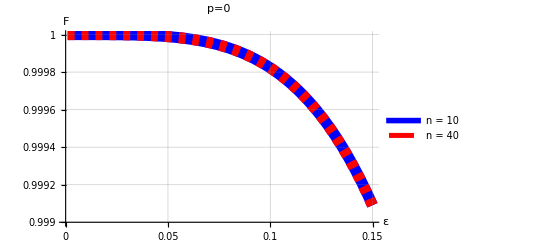

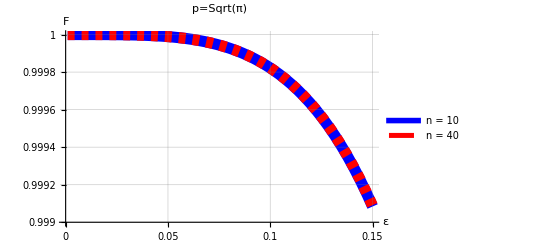

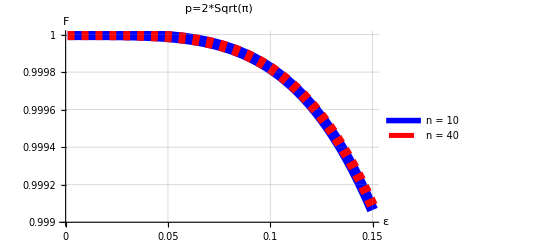

```mathematica
Show[PFp010,PFp040]
Show[PFpSqrtPi10,PFpSqrtPi40]
Show[PFp2SqrtPi10,PFp2SqrtPi40]
```